## Study of single UV limit with join parameterisation

## Parameterisations

```mathematica
SphericalMap[x1_,x2_,x3_]:=Module[
{r=x1/(1-x1),θ=x2 π,ϕ=x3 2π,y,drOverdx=1/(x1-1)^2},
<|"vector"->{
r Sin[θ]Cos[ϕ],
r Sin[θ]Sin[ϕ],
r Cos[θ]
},
"jacobian"->(π) (2π)drOverdx r^2 Sin[θ]
|>
]
```

```mathematica
Solve[rv-x1/(1-x1)==0,{x1}]
```

{{x1→rv/(rv+1)}}

```mathematica
InvSphericalMap[x_,y_,z_]:=Module[
{r,θ,ϕ,xr,sphCoord,drOverdx},
sphCoord = ToSphericalCoordinates[{x,y,z}];
r=sphCoord⟦1⟧;
θ=sphCoord⟦2⟧;
ϕ=sphCoord⟦3⟧;
xr=r/(r+1);
drOverdx=1/(xr-1)^2;
<|"xs"->{
xr,
θ/π,
Mod[ϕ,2π]/(2π)
},
"inv_jacobian"->1/((π) (2π)drOverdx r^2 Sin[θ])
|>
]
```

Test the inverse map

```mathematica
Manipulate[{
(InvSphericalMap@@SphericalMap[x1,x2,x3]["vector"])["inv_jacobian"]*SphericalMap[x1,x2,x3]["jacobian"],
(InvSphericalMap@@SphericalMap[x1,x2,x3]["vector"])["xs"]-{x1,x2,x3}

}/.{x1->xm1,x2->xm2,x3->xm3},
{{xm1,0.2},0.,1.},
{{xm2,0.3},0.,1.},
{{xm3,0.4},0.,1.}
]
```

```mathematica
JointSphericalMap2Loop[x1_,x2_,x3_,x4_,x5_,x6_]:=Module[
{r=x1/(1-x1),θ1=x2 π,ϕ1=x3 2π,θ2=x5 π,ϕ2=x6 2π,y,drOverdx=x1/(1-x1)^3,r1,r2},
r2=r x4 ;
r1=r-r2;
<|"vectorA"->{
r1 Sin[θ1]Cos[ϕ1],
r1 Sin[θ1]Sin[ϕ1],
r1 Cos[θ1]
},
"vectorB"->{
r2 Sin[θ2]Cos[ϕ2],
r2 Sin[θ2]Sin[ϕ2],
r2 Cos[θ2]
},
"jacobian"->(π) (2π)(π) (2π)drOverdx r1^2 Sin[θ1] r2^2 Sin[θ2]
|>
]
```

```mathematica
Solve[{x1/(1-x1)x4-rv2==0,x1/(1-x1)(1-x4)-rv1==0},{x1,x4}]
```

{{x1→(rv1+rv2)/(rv1+rv2+1),x4→rv2/(rv1+rv2)}}

```mathematica
InvJointSphericalMap2Loop[x1_,y1_,z1_,x2_,y2_,z2_]:=Module[
{r1,θ1,ϕ1,r2,θ2,ϕ2,y,drOverdx,xv1,xv4,sphCoord1,sphCoord2},
sphCoord1 = ToSphericalCoordinates[{x1,y1,z1}];
r1=sphCoord1⟦1⟧;
θ1=sphCoord1⟦2⟧;
ϕ1=sphCoord1⟦3⟧;
sphCoord2 = ToSphericalCoordinates[{x2,y2,z2}];
r2=sphCoord2⟦1⟧;
θ2=sphCoord2⟦2⟧;
ϕ2=sphCoord2⟦3⟧;
xv1=(r1+r2)/(r1+r2+1);
xv4=r2/(r1+r2);
drOverdx=xv1/(1-xv1)^3;
<|"xs"->{
xv1,
θ1/π,
Mod[ϕ1,2π]/(2π),
xv4,
θ2/π,
Mod[ϕ2,2π]/(2π)
},
"inv_jacobian"->1/((π) (2π)(π) (2π)drOverdx r1^2 Sin[θ1] r2^2 Sin[θ2])
|>
]
```

```mathematica
Manipulate[{
(InvJointSphericalMap2Loop@@Join[
JointSphericalMap2Loop[x1,x2,x3,x4,x5,x6]["vectorA"],
JointSphericalMap2Loop[x1,x2,x3,x4,x5,x6]["vectorB"]
])["inv_jacobian"]*JointSphericalMap2Loop[x1,x2,x3,x4,x5,x6]["jacobian"],
(InvJointSphericalMap2Loop@@Join[
JointSphericalMap2Loop[x1,x2,x3,x4,x5,x6]["vectorA"],
JointSphericalMap2Loop[x1,x2,x3,x4,x5,x6]["vectorB"]
])["xs"]-{x1,x2,x3,x4,x5,x6}
}/.{x1->xm1,x2->xm2,x3->xm3,x4->xm4,x5->xm5,x6->xm6},
{{xm1,0.2},0.,1.},
{{xm2,0.3},0.,1.},
{{xm3,0.4},0.,1.},
{{xm4,0.2},0.,1.},
{{xm5,0.3},0.,1.},
{{xm6,0.4},0.,1.}
]
```

## Integrand definition

Let the integrator always display error message as it provides an estimate of the integral error.

```mathematica
Off[General::stop]
```

```mathematica
Integrand[k_,l_,p_,M_]:=((k.p)^2*l.p)/(((k+p).(k+p)+M^2)^2*((l+p).(l+p)+M^2)^2*((k+l).(k+l)+M^2))
```

```mathematica
Do[
Print[
"Stats "<>ToString[statistics]<>" : "<>ToString[
NIntegrate[Integrand[{kx,ky,kz},{lx,ly,lz},{2,2,2},1],
{kx,-∞,∞},{ky,-∞,∞},{kz,-∞,∞},
{lx,-∞,∞},{ly,-∞,∞},{lz,-∞,∞},
Method->"AdaptiveMonteCarlo",PrecisionGoal->4,MaxPoints->statistics,MaxRecursion->1000]
]]
,{statistics,{1000000,5000000}}
]
```

Stats 1000000 : -2103.15

Stats 5000000 : -2292.5

## Probing the double UV limit

This is the first limit identified as problematic with the old disjoint parameterisation

First let’s probe it in momentum space directly

```mathematica
MomSpaceProgression=Table[{UVscaleup,{{1,2,3},{4,5,6}}*10^UVscaleup},{UVscaleup,1.,10.,0.1}];
```

```mathematica
Series[Integrand[{mx,mx,mx},{mx,mx,mx},{2,2,2},1],{mx,∞,0}]
```

O((1/mx)^7)

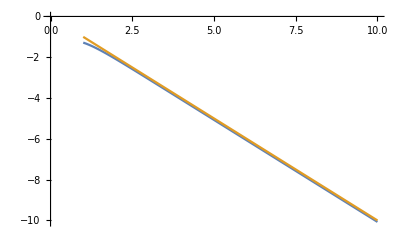

```mathematica
ListLinePlot[
{Table[
{point⟦1⟧,Log[10,Norm[point⟦2⟧⟦1⟧]^3 Norm[point⟦2⟧⟦2⟧]^3 Integrand[point⟦2⟧⟦1⟧,point⟦2⟧⟦2⟧,{2,2,2},1]]},
{point,MomSpaceProgression}
],
Table[
{point⟦1⟧,((slope)*point⟦1⟧)/.{slope->-1}},
{point,MomSpaceProgression}
]
}
]
```

So yes, as expected this is dropping like -7, which means -1 when including the jacobian in momentum space which means it is integrable

Now let us study it in x-space using the disjoint parameterisation

```mathematica
DisjointXSpaceProgression =Table[
{point⟦1⟧,{(InvSphericalMap@@point⟦2⟧⟦1⟧)["xs"],(InvSphericalMap@@point⟦2⟧⟦2⟧)["xs"]}},
{point,MomSpaceProgression}
];
```

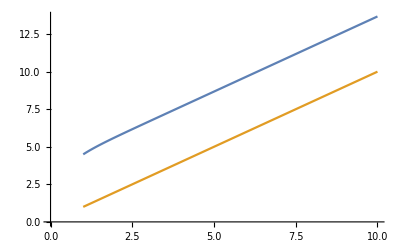

```mathematica
ListLinePlot[
{Table[
{point⟦1⟧,Log[10,
(SphericalMap@@point⟦2⟧⟦1⟧)["jacobian"](SphericalMap@@point⟦2⟧⟦2⟧)["jacobian"]Integrand[(SphericalMap@@point⟦2⟧⟦1⟧)["vector"],(SphericalMap@@point⟦2⟧⟦2⟧)["vector"],{2,2,2},1]]},
{point,DisjointXSpaceProgression}
],
Table[
{point⟦1⟧,((slope)*point⟦1⟧)/.{slope->1}},
{point,MomSpaceProgression}
]
}
]
```

Which confirms that the integrand weight, including the jacobian of the disjoint spherical parameterisation, is blowing up linearly in the UV, so that this is an integrable singularity!

Let us now see how the join parameterisation remedies this

```mathematica
JointXSpaceProgression =Table[
{point⟦1⟧,(InvJointSphericalMap2Loop@@Join[point⟦2⟧⟦1⟧,point⟦2⟧⟦2⟧])["xs"]},
{point,MomSpaceProgression}
];
```

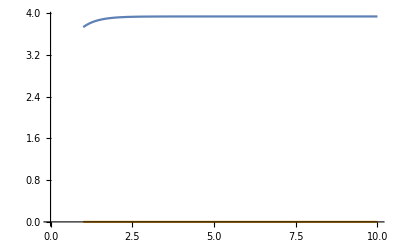

```mathematica
ListLinePlot[
{Table[
{point⟦1⟧,Log[10,
(JointSphericalMap2Loop@@point⟦2⟧)["jacobian"]
Integrand[
(JointSphericalMap2Loop@@point⟦2⟧)["vectorA"],
(JointSphericalMap2Loop@@point⟦2⟧)["vectorB"],
{2,2,2},1]]},
{point,JointXSpaceProgression}
],
Table[
{point⟦1⟧,((slope)*point⟦1⟧)/.{slope->0}},
{point,MomSpaceProgression}
]
}
]
```

Yeah It goes like a constant now! :)

## Probing the single k-UV limit

First let’s probe it in momentum space directly

```mathematica
MomSpaceProgression=Table[{UVscaleup,{{1,2,3}*10^UVscaleup,{4,5,6}}},{UVscaleup,1.,15.,0.1}];
```

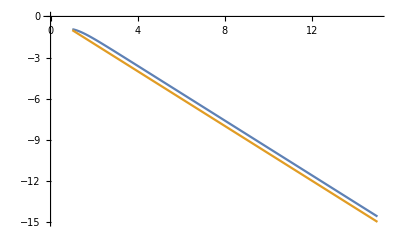

```mathematica
ListLinePlot[
{Table[
{point⟦1⟧,Log[10,Norm[point⟦2⟧⟦1⟧]^3 Norm[point⟦2⟧⟦2⟧]^3 Integrand[point⟦2⟧⟦1⟧,point⟦2⟧⟦2⟧,{2,2,2},1]]},
{point,MomSpaceProgression}
],
Table[
{point⟦1⟧,((slope)*point⟦1⟧)/.{slope->-1}},
{point,MomSpaceProgression}
]
}
]
```

Old disjoint parameterisation

```mathematica
DisjointXSpaceProgression =Table[
{point⟦1⟧,{(InvSphericalMap@@point⟦2⟧⟦1⟧)["xs"],(InvSphericalMap@@point⟦2⟧⟦2⟧)["xs"]}},
{point,MomSpaceProgression}
];
```

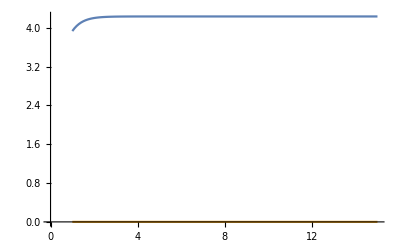

```mathematica
ListLinePlot[
{Table[
{point⟦1⟧,Log[10,
(SphericalMap@@point⟦2⟧⟦1⟧)["jacobian"](SphericalMap@@point⟦2⟧⟦2⟧)["jacobian"]Integrand[(SphericalMap@@point⟦2⟧⟦1⟧)["vector"],(SphericalMap@@point⟦2⟧⟦2⟧)["vector"],{2,2,2},1]]},
{point,DisjointXSpaceProgression}
],
Table[
{point⟦1⟧,((slope)*point⟦1⟧)/.{slope->-0}},
{point,MomSpaceProgression}
]
}
]
```

New joint parameterisation

```mathematica
JointXSpaceProgression =Table[
{point⟦1⟧,(InvJointSphericalMap2Loop@@Join[point⟦2⟧⟦1⟧,point⟦2⟧⟦2⟧])["xs"]},
{point,MomSpaceProgression}
];
```

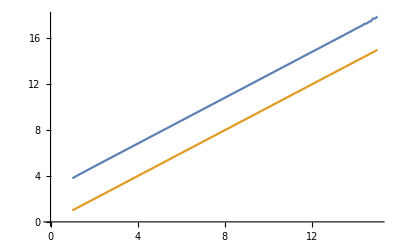

```mathematica
ListLinePlot[
{Table[
{point⟦1⟧,Log[10,
(JointSphericalMap2Loop@@point⟦2⟧)["jacobian"]
Integrand[
(JointSphericalMap2Loop@@point⟦2⟧)["vectorA"],
(JointSphericalMap2Loop@@point⟦2⟧)["vectorB"],
{2,2,2},1]]},
{point,JointXSpaceProgression}
],
Table[
{point⟦1⟧,((slope)*point⟦1⟧)/.{slope->1}},
{point,MomSpaceProgression}
]
}
]
```

## Probing the single l-UV limit

First let’s probe it in momentum space directly

```mathematica
MomSpaceProgression=Table[{UVscaleup,{{1,2,3},{4,5,6}*10^UVscaleup}},{UVscaleup,1.,15.,0.1}];
```

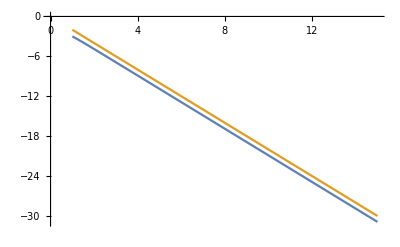

```mathematica
ListLinePlot[
{Table[
{point⟦1⟧,Log[10,Norm[point⟦2⟧⟦1⟧]^3 Norm[point⟦2⟧⟦2⟧]^3 Integrand[point⟦2⟧⟦1⟧,point⟦2⟧⟦2⟧,{2,2,2},1]]},
{point,MomSpaceProgression}
],
Table[
{point⟦1⟧,((slope)*point⟦1⟧)/.{slope->-2}},
{point,MomSpaceProgression}
]
}
]
```

Old disjoint parameterisation

```mathematica
DisjointXSpaceProgression =Table[
{point⟦1⟧,{(InvSphericalMap@@point⟦2⟧⟦1⟧)["xs"],(InvSphericalMap@@point⟦2⟧⟦2⟧)["xs"]}},
{point,MomSpaceProgression}
];
```

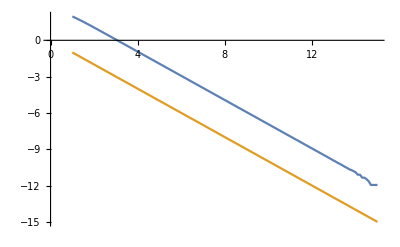

```mathematica
ListLinePlot[
{Table[
{point⟦1⟧,Log[10,
(SphericalMap@@point⟦2⟧⟦1⟧)["jacobian"](SphericalMap@@point⟦2⟧⟦2⟧)["jacobian"]Integrand[(SphericalMap@@point⟦2⟧⟦1⟧)["vector"],(SphericalMap@@point⟦2⟧⟦2⟧)["vector"],{2,2,2},1]]},
{point,DisjointXSpaceProgression}
],
Table[
{point⟦1⟧,((slope)*point⟦1⟧)/.{slope->-1}},
{point,MomSpaceProgression}
]
}
]
```

New joint parameterisation

```mathematica
JointXSpaceProgression =Table[
{point⟦1⟧,(InvJointSphericalMap2Loop@@Join[point⟦2⟧⟦1⟧,point⟦2⟧⟦2⟧])["xs"]},
{point,MomSpaceProgression}
];
```

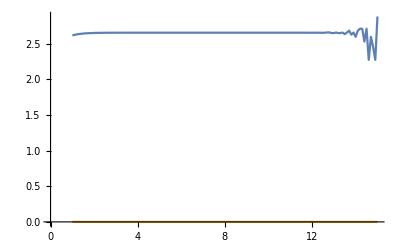

```mathematica
ListLinePlot[
{Table[
{point⟦1⟧,Log[10,
(JointSphericalMap2Loop@@point⟦2⟧)["jacobian"]
Integrand[
(JointSphericalMap2Loop@@point⟦2⟧)["vectorA"],
(JointSphericalMap2Loop@@point⟦2⟧)["vectorB"],
{2,2,2},1]]},
{point,JointXSpaceProgression}
],
Table[
{point⟦1⟧,((slope)*point⟦1⟧)/.{slope->0}},
{point,MomSpaceProgression}
]
}
]
```